```mathematica
Remove[PeterBurbery`UndirectedGraphs`IndependencePolynomial]
```

```mathematica
IndependencePolynomial[PetersenGraph[]]
```

1+10 x+30 x^2+30 x^3+5 x^4

```mathematica
IndependencePolynomial[PetersenGraph[10,12]]
```

1+20 x+160 x^2+660 x^3+1510 x^4+1912 x^5+1240 x^6+320 x^7+5 x^8

```mathematica
?CoboundaryPolynomial
```

```mathematica
??PeterBurbery`UndirectedGraphs`IndependencePolynomial
```

```mathematica
Do[Quiet[Get/@FileNames["*.wl","C:\\Users\\Peter\\OneDrive - Marshall University\\GitHub\\undirected-graphs-paclet\\Undirected Graphs\\Kernel"];,Get::noopen],4]
```

AlternatingTreeGraph::shdw: Symbol AlternatingTreeGraph appears in multiple contexts {PeterBurbery`UndirectedGraphs`,Global`}; definitions in context PeterBurbery`UndirectedGraphs` may shadow or be shadowed by other definitions.

```mathematica
?CoboundaryPolynomial
```

```mathematica
CoboundaryPolynomial[PetersenGraph[]]
```

q^9+15 q^8 (-1+t)+105 q^7 (-1+t)^2+455 q^6 (-1+t)^3+3 q^5 (-1+t)^4 (451+4 t)+q^4 (-1+t)^5 (2861+130 t)+15 q^3 (-1+t)^6 (285+38 t+2 t^2)+15 q^2 (-1+t)^7 (287+86 t+13 t^2+t^3)+q (-1+t)^8 (2606+1498 t+471 t^2+95 t^3+10 t^4)+(-1+t)^9 (704+696 t+390 t^2+155 t^3+45 t^4+9 t^5+t^6)

```mathematica
Expand@CoboundaryPolynomial[PetersenGraph[]]
```

-704+2606 q-4305 q^2+4275 q^3-2861 q^4+1353 q^5-455 q^6+105 q^7-15 q^8+q^9+5640 t-19350 q t+28845 q^2 t-25080 q^3 t+14175 q^4 t-5400 q^5 t+1365 q^6 t-210 q^7 t+15 q^8 t-19470 t^2+61455 q t^2-81570 q^2 t^2+60735 q^3 t^2-27960 q^4 t^2+8070 q^5 t^2-1365 q^6 t^2+105 q^7 t^2+37435 t^3-107665 q t^3+124935 q^2 t^3-77130 q^3 t^3+27310 q^4 t^3-5340 q^5 t^3+455 q^6 t^3-42930 t^4+110970 q t^4-109515 q^2 t^4+53175 q^3 t^4-13005 q^4 t^4+1305 q^5 t^4+28584 t^5-64872 q t^5+51765 q^2 t^5-17700 q^3 t^5+2211 q^4 t^5+12 q^5 t^5-9100 t^6+17010 q t^6-9345 q^2 t^6+1305 q^3 t^6+130 q^4 t^6-45 t^7+810 q t^7-1155 q^2 t^7+390 q^3 t^7+540 t^8-810 q t^8+240 q^2 t^8+30 q^3 t^8+80 t^9-170 q t^9+90 q^2 t^9-6 t^10-9 q t^10+15 q^2 t^10-15 t^11+15 q t^11-10 t^12+10 q t^12+t^15

```mathematica
GraphData["PetersenGraph","CoboundaryPolynomial"][q,t]
```

-704+2606 q-4305 q^2+4275 q^3-2861 q^4+1353 q^5-455 q^6+105 q^7-15 q^8+q^9+5640 t-19350 q t+28845 q^2 t-25080 q^3 t+14175 q^4 t-5400 q^5 t+1365 q^6 t-210 q^7 t+15 q^8 t-19470 t^2+61455 q t^2-81570 q^2 t^2+60735 q^3 t^2-27960 q^4 t^2+8070 q^5 t^2-1365 q^6 t^2+105 q^7 t^2+37435 t^3-107665 q t^3+124935 q^2 t^3-77130 q^3 t^3+27310 q^4 t^3-5340 q^5 t^3+455 q^6 t^3-42930 t^4+110970 q t^4-109515 q^2 t^4+53175 q^3 t^4-13005 q^4 t^4+1305 q^5 t^4+28584 t^5-64872 q t^5+51765 q^2 t^5-17700 q^3 t^5+2211 q^4 t^5+12 q^5 t^5-9100 t^6+17010 q t^6-9345 q^2 t^6+1305 q^3 t^6+130 q^4 t^6-45 t^7+810 q t^7-1155 q^2 t^7+390 q^3 t^7+540 t^8-810 q t^8+240 q^2 t^8+30 q^3 t^8+80 t^9-170 q t^9+90 q^2 t^9-6 t^10-9 q t^10+15 q^2 t^10-15 t^11+15 q t^11-10 t^12+10 q t^12+t^15

```mathematica
CodeEquivalentQ[Expand@CoboundaryPolynomial[PetersenGraph[]],GraphData["PetersenGraph","CoboundaryPolynomial"][q,t]]
```

True

```mathematica
ResistanceMatrix[PetersenGraph[]]
```

SparseArray[…]

```mathematica
ReliabilityPolynomial[PetersenGraph[]]
```

-(-1+p)^9 (1+9 p+45 p^2+155 p^3+390 p^4+696 p^5+704 p^6)

```mathematica
Remove[Global`TriangularGridGraph]
```

```mathematica
Remove[Global`PositiveIntegerQ]
```

```mathematica
Remove[Global`VertexCoordinateList]
```

```mathematica
ResourceFunction["PacletizeResourceFunction"][PacletUninstall,"VertexCoordinateList"]
```

```mathematica
ResourceFunction["PacletizeResourceFunction"][PacletUninstall,"AlternatingTreeGraph"]
```

```mathematica
Quit[]
```

```mathematica
PositiveIntegerQ[1]
```

True

```mathematica
PositiveIntegerQ[0]
```

False

```mathematica
ResourceFunction["PacletizeResourceFunction"][PacletUninstall,"VertexCoordinateList"]
```

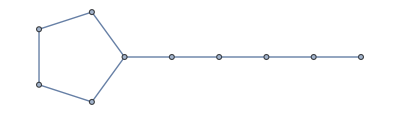

```mathematica
TadpoleGraph[{5,5}]
```

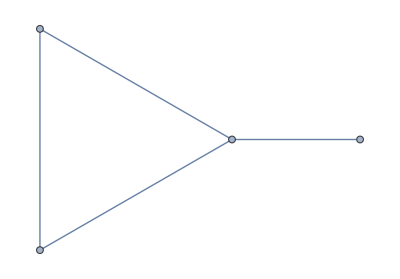
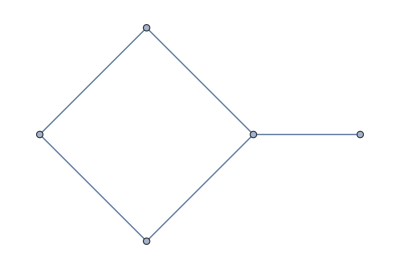
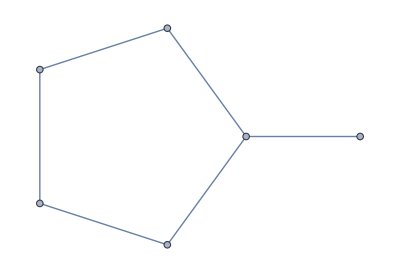
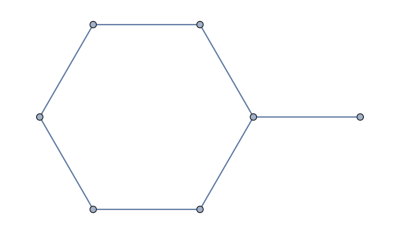
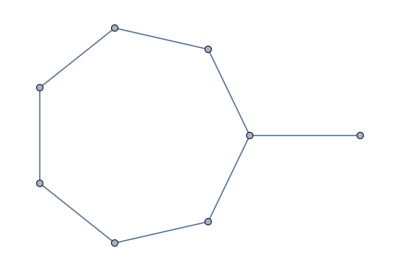
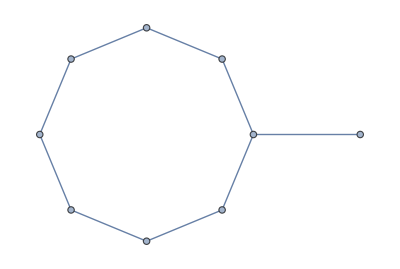
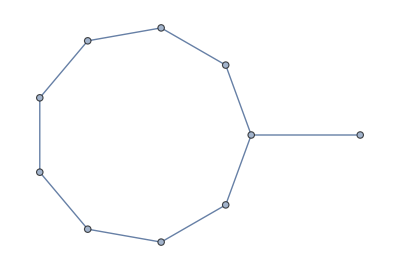
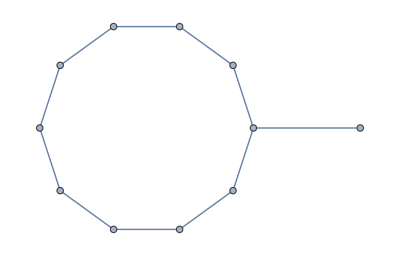

```mathematica
Table[PanGraph[n],{n,3,10}]
```

```mathematica
$ContextPath
```

{PeterBurbery`UndirectedGraphs`,WordGraph`,WordCloudFromNames`,WolfieSay`,WinterSolstice`,WikidataGeoPosition`,VennDiagram`,UnsortedComplement`,UnitSystemTransform`,UndirectedGraphToMixedGraph`,SymbolicIndexedArray`,SymbolDependencyGraph`,SymbolDependencies`,SummarizeDefinition`,StoneyUnitConversion`,StirlingsFormula`,SIConstantConvert`,ShuffleOrder`,Shuffle`,SetPartitions`,SessionHistoryNotebook`,SentenceCount`,SemiEulerianGraphQ`,RuleReverse`,RowSpace`,RhumbLineDistance`,ReadableForm`,RandomWeightedGraph`,RandomPolynomial`,RandomMixedGraph`,RandomMaze`,RandomComposite`,RandomBinaryTree`,QueensGraph`,PrintDefinitions`,PrettyForm`,PositionQ`,PlanckUnitConversion`,PhysicalQuantityData`,PacletizeResourceFunction`,OrderlessCombinations`,Nullity`,NinePointCubic`,NextLeapYear`,MultisetDerangements`,MixedEulerianGraphQ`,MapCases`,LiouvilleNumber`,KSetPartitions`,InverseFactorial`,HighlightTextDifferences`,GraphPathMatrix`,GeoSpatialDistanceList`,GeoSpatialDistance`,GeoCommunityGraphPlot`,FromCamelCase`,FourPointParabolas`,FivePointConic`,FirstWebImage`,ExifAltitude`,EulerizeGraph`,DistanceFromEarthCenter`,ContainsMissing`,ConsistentAugmentedMatrixQ`,ConicProperties`,ColumnSpace`,ColorGraphVertices`,ColorGraphEdges`,CoefficientMatrix`,CatalanUnrank`,CatalanRank`,CartesianProduct`,CanonicalDimensionalProduct`,BirdSay`,BirdChat`,BalancedTernary`,AugmentedMatrix`,Arity`,AreaBetweenCurves`,ArcLengthIntegral`,AntiSimplify`,AngleBetweenPlanes`,AlternatingTreeGraph`,AIAssistant`,AbundantNumberQ`,System`,Global`}

```mathematica
Information["PeterBurbery`UndirectedGraphs`*"]
```

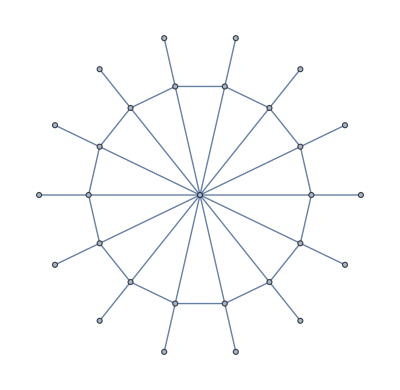

```mathematica
HelmGraph[14]
```

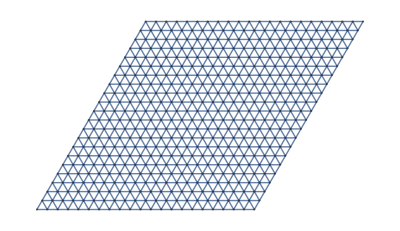

```mathematica
GeneralizedTriangularGridGraph[{21,21}]
```

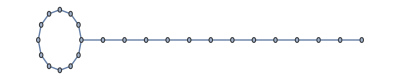

```mathematica
TadpoleGraph[{12,13}]
```

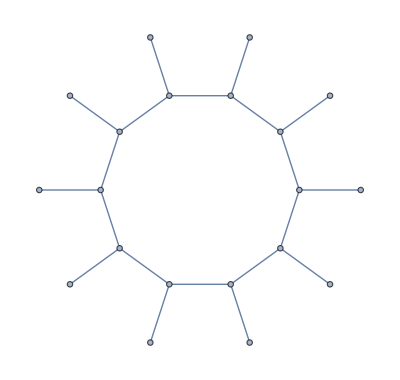

```mathematica
SunletGraph[10]
```

```mathematica
RankPolynomial[KayakPaddleGraph[{12,13,14}]]
```

(1+x)^14 (1+25 x+300 x^2+2300 x^3+12650 x^4+53130 x^5+177100 x^6+480700 x^7+1081575 x^8+2042975 x^9+3268760 x^10+x^11 (4457400+y)+x^12 (5200299+14 y)+176 x^18 (2717+15 y)+22 x^14 (202605+16 y)+22 x^21 (520+23 y)+6 x^22 (299+24 y)+66 x^16 (30940+27 y)+33 x^17 (32721+76 y)+11 x^15 (297128+85 y)+x^13 (5200286+90 y)+11 x^20 (4641+110 y)+11 x^19 (15860+189 y)+x^23 (156+25 y+y^2))

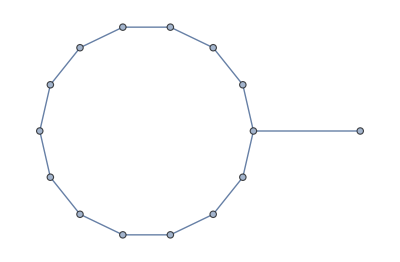

```mathematica
PanGraph[14]
```

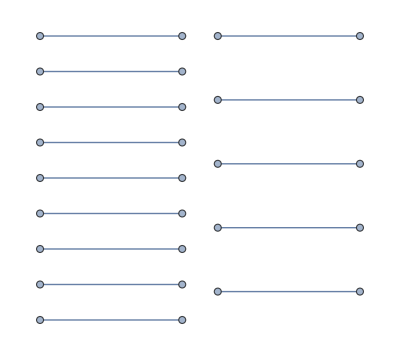

```mathematica
LadderRungGraph[14]
```

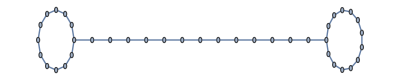

```mathematica
KayakPaddleGraph[{12,13,14}]
```

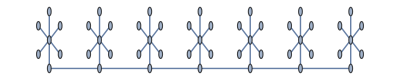

```mathematica
FirecrackerGraph[{7,7}]
```

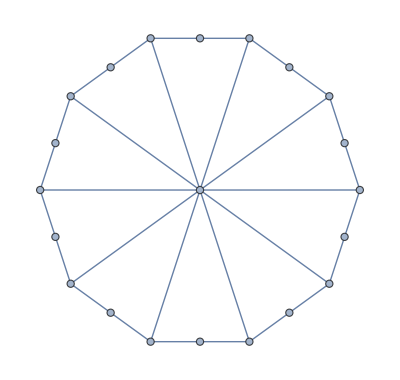

```mathematica
GearGraph[10]
```

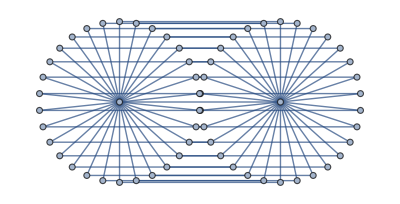

```mathematica
BookGraph[30]
```

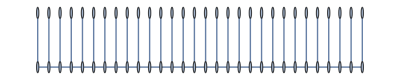

```mathematica
CombGraph[30]
```

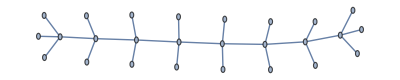

```mathematica
AlternatingTreeGraph[10]
```

```mathematica
Remove[AlternatingTreeGraph`AlternatingTreeGraph]
```

Remove::rmptc: Symbol AlternatingTreeGraph`AlternatingTreeGraph is Protected and cannot be removed.

```mathematica
Unprotect[AlternatingTreeGraph`AlternatingTreeGraph]
```

{AlternatingTreeGraph`AlternatingTreeGraph}

```mathematica
Remove[AlternatingTreeGraph`AlternatingTreeGraph]
```

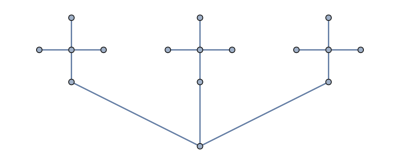

```mathematica
BananaTreeGraph[{3,5}]
```

```mathematica
SetOptions[Graph,VertexLabels->Automatic];
```

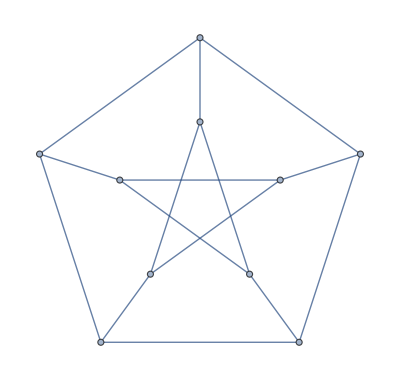

```mathematica
PetersenGraph[]
```

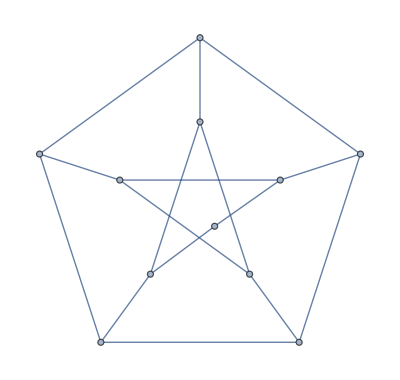

```mathematica
VertexInsert[PetersenGraph[],First[EdgeList[PetersenGraph[]]],11]
```

```mathematica
?VertexInsert
```

```mathematica
?GraphicalDegreeSequenceQ
```

```mathematica
?VertexCoordinateList
```

```mathematica
?Girth
```

```mathematica
?Girth
```

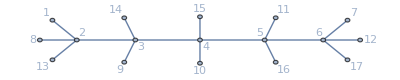

```mathematica
AlternatingTreeGraph[7,VertexLabels->Automatic]
```